```mathematica
G1[J_,q_] := Sqrt[J^2+2J*q*Cos[k]];
```

```mathematica
G2[J_,q_,J2_] := Sqrt[J^2+2J*(q*Cos[k]+J2*Cos[2k])];
```

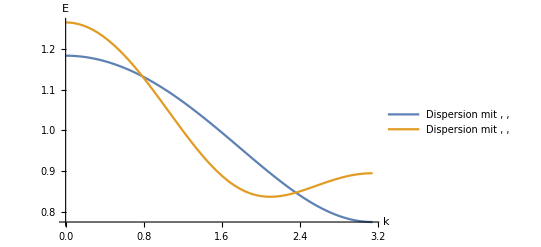

```mathematica
Plot[{G1[1,0.2],G2[1,0.2,0.1]},{k,0,Pi},AxesLabel->{k,"E"},PlotLegends->Placed[{"Dispersion mit , , ", "Dispersion  mit , , "},Above]]
```

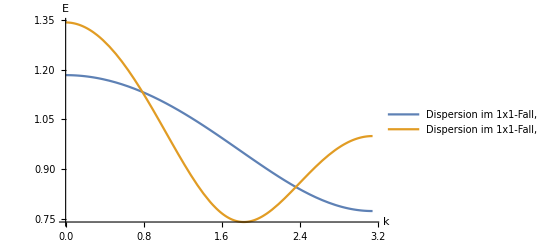

```mathematica
Plot[{G1[1,0.2],G2[1,0.2,0.2]},{k,0,Pi},AxesLabel->{k,"E"},PlotLegends->Placed[{"Dispersion im 1x1-Fall, mit , ", "Dispersion im 1x1-Fall, mit , , "},Above]]
```